{{A1→InterpolatingFunction[{{0., 25.}}, <>],A2→InterpolatingFunction[{{0., 25.}}, <>]}}

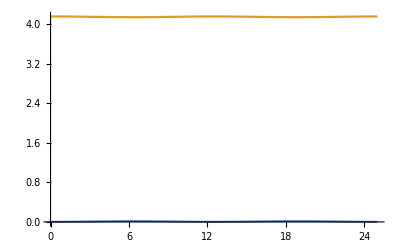

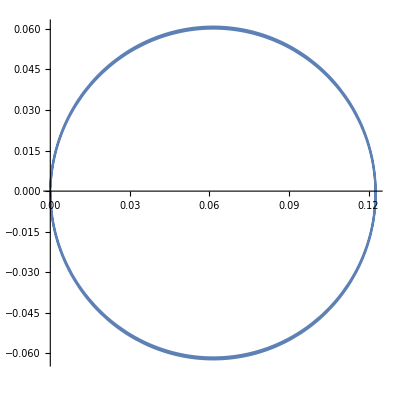

```mathematica
Clear["Global`*"]

n1=1.6;
n2=1.6;
λ=1064*10^-9;
deff=0.85 10^-12;(*m/V*)
ε0=8.85 10^-12;(*F/m*)
S=Pi 100^2/4 10^-12;(*m^2*)
c=3 10^8;(*m/s*)
L=2.5 10^-2*1000;
P=0.1;
Δk=0.5;
Esgs=Sqrt[P*2/(S n1^2 ε0 c)]/30000;

σ1=2  Pi  (2 Pi/λ) (2 deff)/(n1^2) 300;
σ2= Pi  (2 Pi/(λ/2)) (2 deff)/(n2^2) 300;
sol=NDSolve[
{A1'[z]==-I σ1 Conjugate[ A1[z]] A2[z] Exp[-I Δk z],
A2'[z]==-I σ2 A1[z]^2  Exp[I Δk z],A2[0]==0,A1[0]==Esgs},{A1,A2},{z,0,L}]
Plot[{Abs[A2[x]/.sol[[1]]]^2,Abs[A1[x]/.sol[[1]]]^2},{x,0,L},PlotRange->All]
ParametricPlot[{Re[A2[x]/.sol[[1]]],Im[A2[x]/.sol[[1]]]},{x,0,L}]
```

{{A1→InterpolatingFunction[{{0., 13.9626}}, <>],A2→InterpolatingFunction[{{0., 13.9626}}, <>]}}

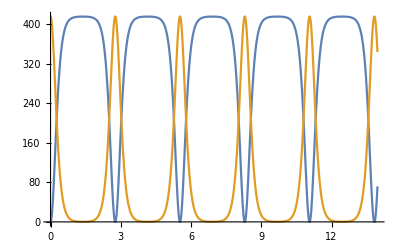

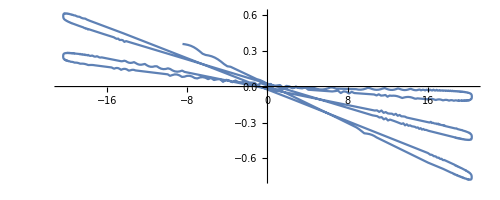

```mathematica
Clear["Global`*"]

n1=1.6;
n2=1.6;
λ=1064*10^-9;
deff=30 10^-12;(*m/V*)
ε0=8.85 10^-12;(*F/m*)
S=Pi 100^2/4 10^-12;(*m^2*)
c=3 10^8;(*m/s*)
L=2.5 10^-2*1000;
P=10;
Δk=4500;
Esgs=Sqrt[P*2/(S n1^2 ε0 c)]/30000;
ld=(7-0.0187)*10^-4;
Nd=20000;

σ1=2  Pi  (2 Pi/λ) (2 deff)/(n1^2) 300;
σ2= Pi  (2 Pi/(λ/2)) (2 deff)/(n2^2) 300;
sol=NDSolve[
{A1'[z]==-I σ1 Conjugate[ A1[z]] A2[z] Exp[-I Δk z]*Power[-1,Floor[z/ld]],
A2'[z]==-I σ2 A1[z]^2  Exp[I Δk z]*Power[-1,Floor[z/ld]],
A2[0]==0,A1[0]==Esgs},{A1,A2},{z,0,Nd ld}]
Plot[{Abs[A2[x]/.sol[[1]]]^2,Abs[A1[x]/.sol[[1]]]^2},{x,0,Nd ld},PlotRange->All]
ParametricPlot[{Re[A2[x]/.sol[[1]]],Im[A2[x]/.sol[[1]]]},{x,0,Nd ld}]
```